# Definitions of tensor.

This does not rely on the main FeynGrav package.
It serves only to generate libraries.

```mathematica
<<FeynCalc`
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

## I tensor

The following command takes a single integer number and returns a list of 2n variables.

```mathematica
dummyArray=n↦Flatten[(x↦{ToExpression["m"<>ToString[x]],ToExpression["n"<>ToString[x]]})/@Range[n]];
```

This command takes a list of even number of elements, splits it in pairs, and make a metric of each pair.

```mathematica
MTDWrapper=x↦Times@@MTD@@@Partition[x,2];
```

This command takes two lists. The first one is the list to be symmetrized. The second one is a list of two elements. The result is a join list. Its first component it the original list; its second component is a list with the given elements begin swapped.

```mathematica
arraySymmetrization={array,argumets}↦Join[array,(array/.{argumets[[1]]->argumets[[2]],argumets[[2]]->argumets[[1]]})];
```

This is the definition of I tensor. It is taken directly from ArXiV:2201.06812.

```mathematica
ITensor = indexArray↦If[Length[indexArray]≠0,Total[1/2^(Length[indexArray]/2)MTDWrapper/@Function[RotateLeft[#,1]]/@Partition[Fold[arraySymmetrization,indexArray,Partition[indexArray,2]],Length[indexArray]]],1];
```

## C tensor

This is the definition of C tensor. It is taken directly from ArXiV:2201.06812.
For the sake of simplicity (and human-readability) it is realized as a few function.

```mathematica
ITensorWrapper={k,x}↦Times@@ITensor/@FoldPairList[TakeDrop,x,2k];
CTensorIndex={n,m}↦Select[Tuples[Range[n],m],Total[#]==n&];
CTensorStructure={indexArray,m}↦Total[Function[1/(Times@@#)ITensorWrapper[#,indexArray]]/@CTensorIndex[Length[indexArray]/2,m]];
CTensorCore=indexArray↦Expand[Total[Function[(-1)^(Length[indexArray]/2+#)/(Factorial[#] 2^#)CTensorStructure[indexArray,#]]/@Range[Length[indexArray]/2]]];
CTensor=indexArray↦If[Length[indexArray]≠0,Expand[Total[1/Factorial[Length[indexArray]/2] CTensorCore[#]&/@(Flatten/@Permutations[Partition[indexArray,2]])]],1];
```

## CIII tensor

CIII definition. In full analogy with the previous case it is taken from ArXiV:2201.06812; and it is separated in a few function to make human-readable.
Its arguments are made in a very specific form.
CIIITensor[{{μ,ν},{α,β},{ρ,σ}},{m1,n1,....}] -- Here {μ,ν},{α,β}, and {ρ,σ} are external indices that present in √-g g^μν g^αβ g^ρσ. Indices m1,n1,... are internal indices which are contracted with h_{m1n1}....

```mathematica
CIIITensorInternalIndices=indexArray↦FoldPairList[TakeDrop,indexArray,2#]&/@(n↦Select[Tuples[Range[0,n],4],Total[#]==n&])[Length[indexArray]/2];
CIIITensorExternalIndices=indexArray↦Join[{{}},Partition[indexArray,2]];
CIIITensorIndices={indexArrayExternal,indexArrayInternal}↦Function[MapThread[Join,{CIIITensorExternalIndices[indexArrayExternal],#}]]/@CIIITensorInternalIndices[indexArrayInternal];
CIIITensorCore = {indexArrayExternal,indexArrayInternal}↦Total[  (indexArray↦(-1)^(Length[indexArrayInternal]/2)(-1)^(-Length[indexArray[[1]]]/2)CTensor[indexArray[[1]]](Times@@ITensor/@indexArray[[2;;]]) )/@CIIITensorIndices[indexArrayExternal,indexArrayInternal]  ];
CIIITensor={indexArrayExternal,indexArrayInternal}↦Expand[Total[1/Factorial[Length[indexArrayInternal]/2](Function[CIIITensorCore[indexArrayExternal,#]]/@Flatten/@Permutations[Partition[indexArrayInternal,2]])]];
```

## Graviton vertex

```mathematica
TTensorGravity={μ,ν,α,β,ρ,σ,λ1,λ2,ρ1,σ1,ρ2,σ2}↦Expand[-MTD[μ,λ1]MTD[ν,λ2]ITensor[{α,β,ρ1,σ1}]ITensor[{ρ,σ,ρ2,σ2}]+MTD[μ,λ1]MTD[ν,λ2]ITensor[{α,ρ,ρ1,σ1}]ITensor[{β,σ,ρ2,σ2}]-2MTD[μ,λ1]MTD[α,λ2]ITensor[{β,ρ,ρ1,σ1}]ITensor[{ν,σ,ρ2,σ2}]+2MTD[μ,λ1]MTD[β,λ2]ITensor[{ν,α,ρ1,σ1}]ITensor[{ρ,σ,ρ2,σ2}]];
GravitonVertexIndices=indexArray↦Flatten[Function[#[[1;;2]]]/@Partition[indexArray,3]];
GravitonVertexCore:=indexArray↦Contract[ⅈ(-2/κ^2)(κ)^(Length[indexArray]/3)/4 CIIITensor[{𝓂1,𝓃1,𝓂2,𝓃2,𝓂3,𝓃3},GravitonVertexIndices[indexArray][[5;;]]]TTensorGravity[Sequence@@Join[{𝓂1,𝓃1,𝓂2,𝓃2,𝓂3,𝓃3},{λ1,λ2},GravitonVertexIndices[indexArray][[;;4]]]]FVD[indexArray[[3]],λ1]FVD[indexArray[[6]],λ2]]
GravitonVertex=indexArray↦Expand[Calc[Total[GravitonVertexCore/@(Flatten/@Permutations[Partition[indexArray,3]])]]];
```

## CI tensor

CI definition.

```mathematica
CITensorInternalIndices=indexArray↦FoldPairList[TakeDrop,indexArray,2#]&/@(n↦Select[Tuples[Range[0,n],2],Total[#]==n&])[Length[indexArray]/2];
CITensorExternalIndices=indexArray↦Join[{{}},Partition[indexArray,2]];
CITensorIndices={indexArrayExternal,indexArrayInternal}↦Function[MapThread[Join,{CITensorExternalIndices[indexArrayExternal],#}]]/@CITensorInternalIndices[indexArrayInternal];
CITensorCore = {indexArrayExternal,indexArrayInternal}↦Total[  (indexArray↦(-1)^(Length[indexArrayInternal]/2)(-1)^(-Length[indexArray[[1]]]/2)CTensor[indexArray[[1]]](Times@@ITensor/@indexArray[[2;;]]) )/@CITensorIndices[indexArrayExternal,indexArrayInternal]  ];
CITensor={indexArrayExternal,indexArrayInternal}↦Expand[Total[1/Factorial[Length[indexArrayInternal]/2](Function[CITensorCore[indexArrayExternal,#]]/@Flatten/@Permutations[Partition[indexArrayInternal,2]])]];
```

## Graviton-Scalar vertex

```mathematica
TTensorGravityScalar={m,n,p,q}↦Calc[-1/2 ITensor[{m,n,𝒶,𝒷}]FVD[p,𝒶]FVD[q,𝒷]];
GravitonScalarVertex=indexArray↦Calc[(ⅈ κ^((Length[indexArray]-2)/2))CITensor[{𝓂,𝓃},indexArray[[;;Length[indexArray]-2]]]TTensorGravityScalar[Sequence@@Join[{𝓂,𝓃},indexArray[[Length[indexArray]-1;;]]]]];
```

# Timings. Do not run without a necessity.

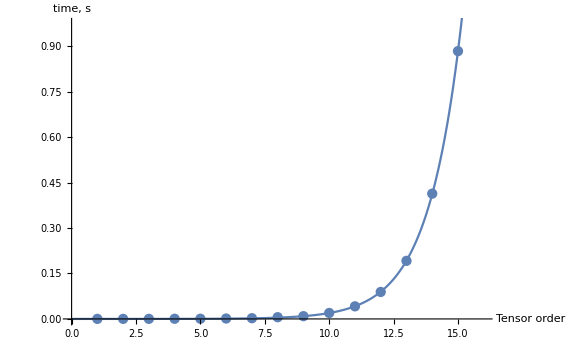

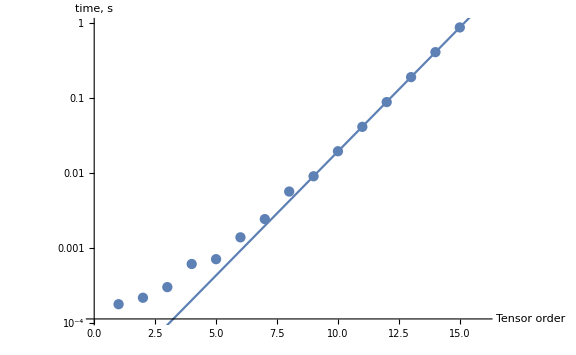

```mathematica
Table[Timing[ITensor[dummyArray[i]]][[1]],{i,1,15}];
τ Exp[t/T]/.FindFit[%,τ Exp[t/T],{τ,T},t];
Show[{ListPlot[%%,ImageSize->Large,AxesLabel->{"Tensor order","time, s"},AxesOrigin->{0,0},PlotRange->{{0,Length[%%]+1},{0,1.1Max[%%]}}],Plot[%,{t,0,Length[%%]+2},PlotLegends->%]}]
Show[{ListLogPlot[%%%,ImageSize->Large,AxesLabel->{"Tensor order","time, s"},AxesOrigin->{0,0},PlotRange->{{0,Length[%%%]+1},{0,1.1Max[%%%]}}],LogPlot[%%,{t,0,Length[%%%]+2},PlotLegends->%%]}]
```

FindFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

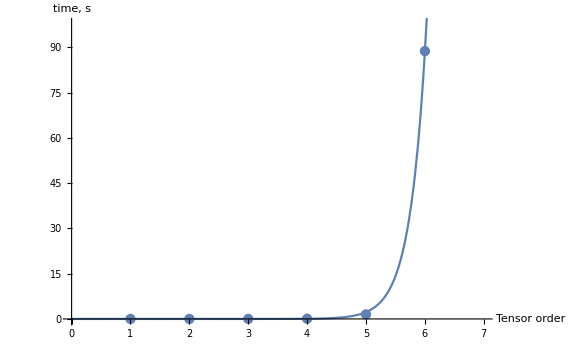

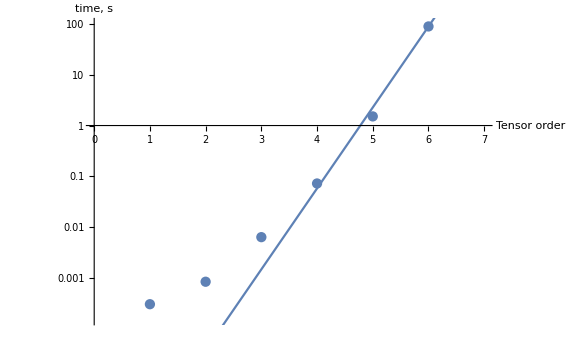

```mathematica
Table[Timing[CTensor[dummyArray[i]]][[1]],{i,1,6}];
τ Exp[t/T]/.FindFit[%,τ Exp[t/T],{τ,T},t];
Show[{ListPlot[%%,ImageSize->Large,AxesLabel->{"Tensor order","time, s"},AxesOrigin->{0,0},PlotRange->{{0,Length[%%]+1},{0,1.1Max[%%]}}],Plot[%,{t,0,Length[%%]+2},PlotLegends->%]}]
Show[{ListLogPlot[%%%,ImageSize->Large,AxesLabel->{"Tensor order","time, s"},AxesOrigin->{0,0},PlotRange->{{0,Length[%%%]+1},{0,1.1Max[%%%]}}],LogPlot[%%,{t,0,Length[%%%]+2},PlotLegends->%%]}]
```

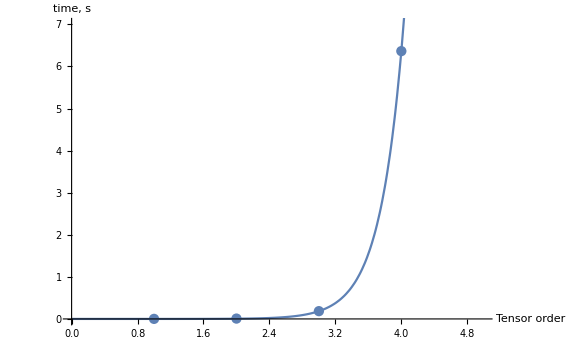

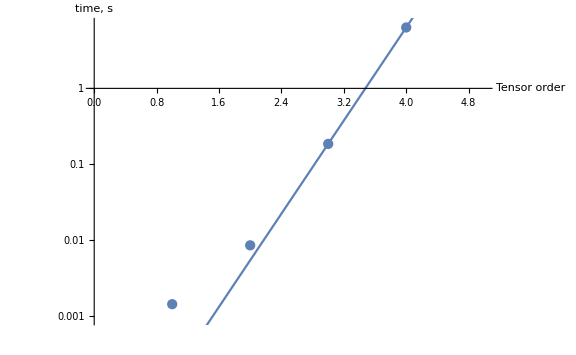

```mathematica
Table[Timing[CIIITensor[{μ,ν,α,β,ρ,σ},dummyArray[i]]][[1]],{i,1,4}];
τ Exp[t/T]/.FindFit[%,τ Exp[t/T],{τ,T},t];
Show[{ListPlot[%%,ImageSize->Large,AxesLabel->{"Tensor order","time, s"},AxesOrigin->{0,0},PlotRange->{{0,Length[%%]+1},{0,1.1Max[%%]}}],Plot[%,{t,0,Length[%%]+2},PlotLegends->%]}]
Show[{ListLogPlot[%%%,ImageSize->Large,AxesLabel->{"Tensor order","time, s"},AxesOrigin->{0,0},PlotRange->{{0,Length[%%%]+1},{0,1.1Max[%%%]}}],LogPlot[%%,{t,0,Length[%%%]+2},PlotLegends->%%]}]
```

{1.18029,29.9595}

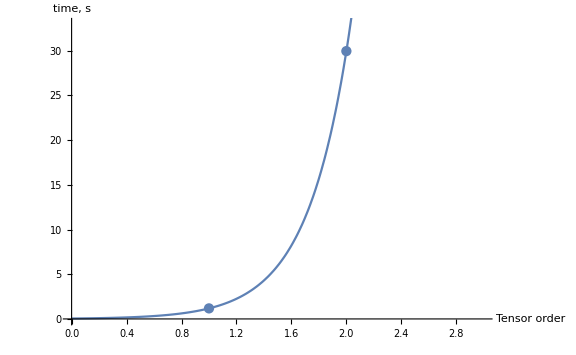

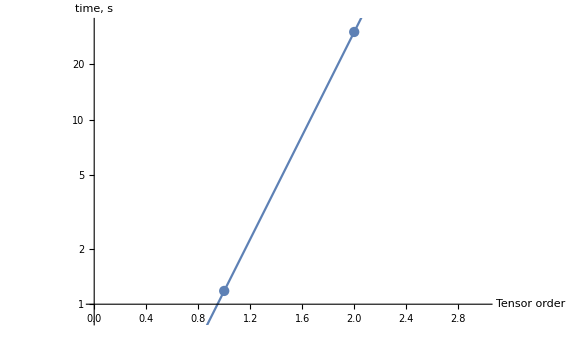

```mathematica
Table[Timing[GravitonVertex[Flatten[Function[{ToExpression["m"<>ToString[#]],ToExpression["n"<>ToString[#]],ToExpression["p"<>ToString[#]]}]/@Range[i]]]][[1]],{i,3,4}]
τ Exp[t/T]/.FindFit[%,τ Exp[t/T],{τ,T},t];
Show[{ListPlot[%%,ImageSize->Large,AxesLabel->{"Tensor order","time, s"},AxesOrigin->{0,0},PlotRange->{{0,Length[%%]+1},{0,1.1Max[%%]}}],Plot[%,{t,0,Length[%%]+2},PlotLegends->%]}]
Show[{ListLogPlot[%%%,ImageSize->Large,AxesLabel->{"Tensor order","time, s"},AxesOrigin->{0,0},PlotRange->{{0,Length[%%%]+1},{0,1.1Max[%%%]}}],LogPlot[%%,{t,0,Length[%%%]+2},PlotLegends->%%]}]
```

# Export

## Code

```mathematica
exportITensor[order_]:=Module[{cursor},
Print["Export of I tensors is initiated."];
For[cursor=1,cursor≤order,cursor++,
ITensor[dummyArray[cursor]]>>"ITensor_"<>ToString[cursor];
Print["Done for order "<>ToString[cursor]];
]
]
```

```mathematica
exportCTensor[order_]:=Module[{cursor},
Print["Export of C tensors is initiated."];
For[cursor=1,cursor≤order,cursor++,
CTensor[dummyArray[cursor]]>>"CTensor_"<>ToString[cursor];
Print["Done for order "<>ToString[cursor]];
]
]
```

```mathematica
exportGravitonVertex[order_] := Module[{cursor}, 
If[order<3,Print["The order must be three or higher!"];Return[]];
Print["Export of graviton vertices is initiated."];
For[cursor=3,cursor≤order,cursor++,
Evaluate[GravitonVertex[Flatten[Function[{ToExpression["m"<>ToString[#]],ToExpression["n"<>ToString[#]],ToExpression["p"<>ToString[#]]}]/@Range[cursor]]]]>>"GravitonVertex_"<>ToString[cursor];
Print["Done for order "<>ToString[cursor]];
]
]
```

```mathematica
exportGravitonScalarVertex[order_]:=Module[{cursor},
	Print["Export of graviton-scalar vertices is initiated."];
	For[cursor=1,cursor<=order,cursor++,
		Evaluate[GravitonScalarVertex[Join[dummyArray[cursor],{p1,p2}]]]>>"GravitonScalarVertex_"<>ToString[cursor];
		Print["Done for order "<>ToString[cursor]];
	]
]
```

```mathematica
exportGravitonVertex[4]
exportGravitonScalarVertex[4]
```

Export of graviton vertices is initiated.

Done for order 3

Done for order 4